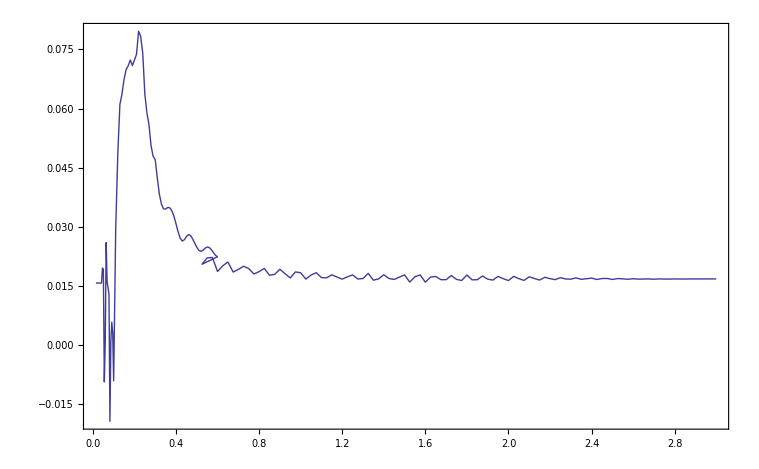

```mathematica
Δ0=0.1;
μ=0.01;
num=144;



f[kx_,ky_]:=Cos[kx]+Cos[ky]-μ;
En[kx_,ky_,Δ_]:=√(f[kx,ky]^2+Δ^2);
v[kx_,ky_,Δ_]:=√((En[kx,ky,Δ]-f[kx,ky])/(2*En[kx,ky,Δ]));

MagZeroTemp[Δ_]:=μ/num^2*∑_(i=0)^(num-1) ∑_(j=0)^(num-1) 1/En[kinit+i*kinc,kinit+j*kinc,Δ];

ThermalMag[β_,Δ_]:=μ/num^2*∑_(i=0)^(num-1) ∑_(j=0)^(num-1) Tanh[β*En[kinit+i*kinc,kinit+j*kinc,Δ]]/En[kinit+i*kinc,kinit+j*kinc,Δ];

ThermalMagSd[β_,Δ_]:=1/num^2*∑_(i=0)^(num-1) ∑_(j=0)^(num-1) Abs[(f[kinit+i*kinc,kinit+j*kinc]/En[kinit+i*kinc,kinit+j*kinc,Δ])*Sech[β*En[kinit+i*kinc,kinit+j*kinc,Δ]]]


kinit=-π;
kfinal=π;
kinc=(kfinal-kinit)/(num-1);
datafile="/home/daneel/workspace/thermaldata/fullavgdata.txt";
avgdata=Drop[Import[datafile,"Table"],1];
ω=avgdata[[All,1]];
mags=avgdata[[All,2]];
Δb=avgdata[[All,4]];
size=Length[ω];
qmagplot=ListPlot[Table[{ω[[i]],mags[[i]]},{i,1,size}],Joined->True,Frame->True,Axes->False,PlotRange->All]
```

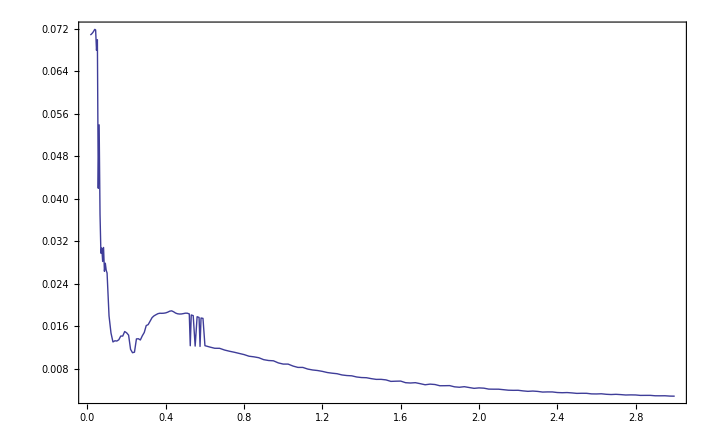

```mathematica
(*Standard Deviation of magnetization in time*)
magfiledir="/home/daneel/workspace/magfiles";
SetDirectory[magfiledir];
filenames=FileNames[];
files=Length[filenames];
sdQ=Table[data=Import[filenames[[i]],"Table"];fname=filenames[[i]];{(StringSplit[fname,"_"][[3]]//ToExpression),(data[[All,2]]//StandardDeviation)},{i,1,files}];
sdQ=Sort[sdQ,#1[[1]]<#2[[1]]&];
ListPlot[sdQ,Frame->True,Axes->False,Joined->True]
```

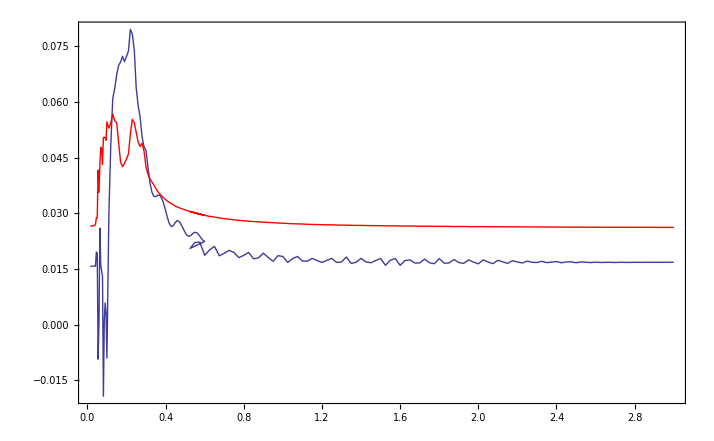

```mathematica
zerotempthmagdata=Table[{ω[[i]],MagZeroTemp[Δb[[i]]]},{i,1,size}];
zerotempplot=ListPlot[zerotempthmagdata,Joined->True,Frame->True,Axes->False,PlotStyle->RGBColor[1,0,0]];
Show[qmagplot,zerotempplot]
Export["/home/daneel/workspace/thermaldata/beta_inf.txt",zerotempthmagdata,"Table"];
```

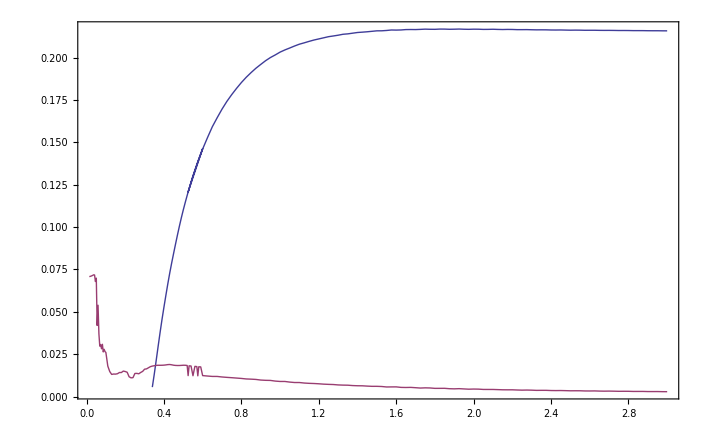

```mathematica
t0=0.26;
ω0=0.28;
ωc=0.32;
temp[ω_]:=t0*(1-Exp[-(ω-ωc)/ω0]);
thermalsds=Table[{ω[[i]],ThermalMagSd[1/temp[ω[[i]]],Δb[[i]]]},{i,44,size}];
ListPlot[{thermalsds,sdQ},Frame->True,Axes->False,Joined->True]
```